### 1. Mathematical problems

```mathematica
1
```

```mathematica
f[x_]:= x^5-302 x^3+893 x^2+1208x-3588
```

```mathematica
FindRoot[f[x], {x, 3}]
```

{x→1.07858}

```mathematica
FindRoot[f[x], {x, -2}]
```

{x→-2.0081}

```mathematica
FindRoot[f[x], {x, 2}]
```

{x→1.98717}

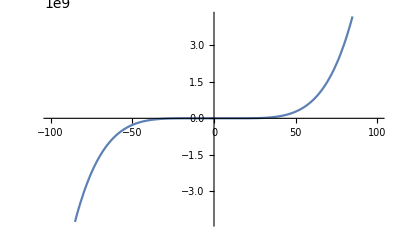

```mathematica
Plot[f[x], {x, -100, 100}]
```

Shows the end behavior of the function.

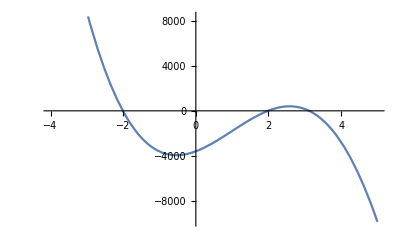

```mathematica
Plot[f[x], {x, -4,5}]
```

Shows the 3 zeros, y intercept, and relative minimum and maximum.

```mathematica
2
```

```mathematica
f[x]=(-3 x^3-3x+7)/(3 x^2-59x-20);
```

```mathematica
NSolve[f[x]==0, x]
```

{{x→-0.53929-1.36839 ⅈ},{x→-0.53929+1.36839 ⅈ},{x→1.07858}}

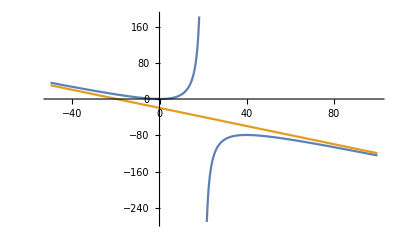

```mathematica
Plot[{f[x], -x-59/3}, {x, -50, 100}]
```

This graph shows the slant asymptote at y = -x-59/3, the vertical asymptote at x = 20, and the end behavior. (Slant asymptote was graphed because it is less obvious at other scales.)

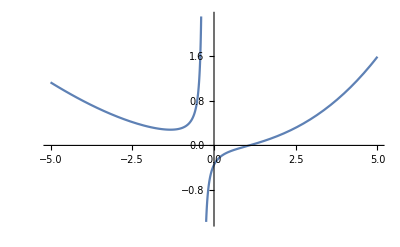

```mathematica
Plot[f[x], {x, -5, 5}]
```

This graph shows the vertical asymptote at x = -1/3, the y intercept, and the zero of the function.

```mathematica
Limit[f[x], x->∞]
```

-∞

```mathematica
Limit[f[x], x->-∞]
```

∞

```mathematica
3
```

```mathematica
f[x]:=(-3 x^3-3x+7+10*2^(.001x))/(3 x^4-27 x^3-2^(.001x))
```

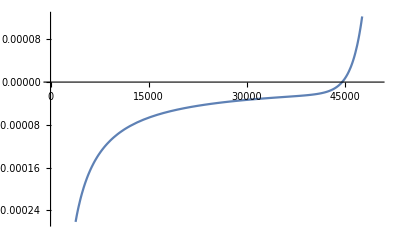

```mathematica
Plot[f[x], {x, 0, 50000}]
```

Shows one zero of the function

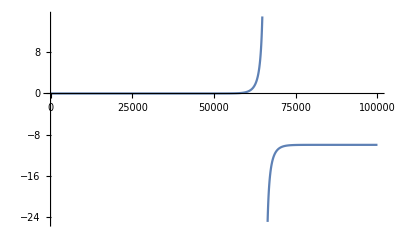

```mathematica
Plot[f[x], {x, 0, 100000}]
```

Shows vertical asymptote and end behavior as the function approaches ∞.

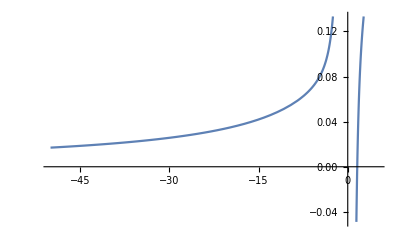

```mathematica
Plot[f[x], {x, -50, 5}]
```

Shows zero of the function and the end behavior as the function approaches -∞.

## II.Sum of Primes

```mathematica
(**)
primeSum[strt_,upperbound_]:= Module[{sum=0,cnt = strt,ansList={},ans={{0,0}},i=1},
While[sum <upperbound,
sum+= Prime[cnt];
If[sum>upperbound,Break[]];
If[PrimeQ[sum], 
AppendTo[ansList,{cnt-strt+1,sum}];
];
cnt++;
];
While[i ≤ Length[ansList],
If[ans[[1,1]]< ansList[[i,1]],
ans[[1]]= ansList[[i]]];
i++;
];
Return[ans]
]
```

```mathematica
longestPrimeSum[upperbound_]:= Module[{cnt= 1, ans={{0,0,0}}, ansList={},i=1, Primes={}},
While[cnt≤ upperbound,
Primes = primeSum[cnt,upperbound];
If[Primes[[1,2]]==0,
Break[]];
AppendTo[ansList,{cnt,Primes[[1,1]],Primes[[1,2]]}];
cnt++;
];
While[i ≤ Length[ansList],
If[ans[[1,2]]< ansList[[i,2]],
ans[[1]]= ansList[[i]]];
i++;
];
Return[ans[[1]]]
]
```

### III. The arclength of a function

```mathematica
a
```

```mathematica
(* creates points at regular x intervals, approximating the function that the points are plotted on as the said interval decreases*)
```

```mathematica
findPoints[func_, interval_, pieces_]:=Module[
{cnt = 0, 
(*distance is the interval between each x value*)
distance = (interval[[2]]-interval[[1]])/(pieces),
list ={}},
While[cnt<=pieces,
(*add points that lie on the function to a list*)
AppendTo[list,{interval[[1]]+distance*cnt, func[interval[[1]]+distance*cnt]}];
cnt++
];
list
]
```

```mathematica
b
```

```mathematica
(*plots the function compared to the list generated by findPoints*)
showLinesegments[func_, interval_, pieces_]:=Module[
{set},
set=findPoints[func, interval, pieces];
Show[
Plot[func[x],{x, interval[[1]], interval[[2]]}, PlotStyle->Blue],
(*plot points in black*)
ListPlot[set, PlotStyle->Black],
(*plot line segments connecting points in findPoints*)
ListLinePlot[set, PlotStyle->Red]
]
]
```

```mathematica
h[x_]:=Cos[4x]^2
```

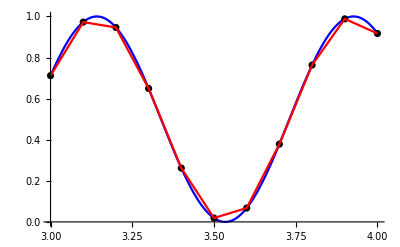

```mathematica
showLinesegments[h, {3,4}, 10]
```

```mathematica
f[x_]:=x^2
```

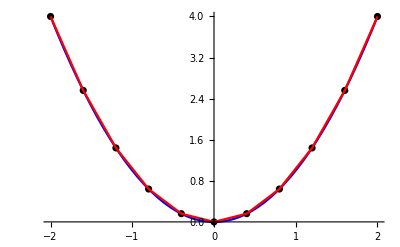

```mathematica
showLinesegments[f, {-2,2}, 10]
```

```mathematica
c
```

```mathematica
(*returns sum of length of line segments between points from findPoints*)
lengthOfCurve[func_, interval_, pieces_]:=Module[
{list, sum=0, cnt=1},
list=findPoints[func, interval, pieces];
While[cnt<Length[list],
(*adding sum from each distance to total sum*)
sum=sum+N@EuclideanDistance[{list[[cnt]]}, {list[[cnt+1]]}];
cnt++
];
sum
]
```

```mathematica
lengthOfCurve[z, {0, 4}, 10]
```

16.8054

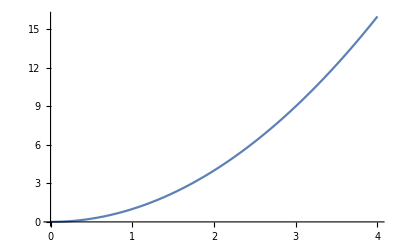

```mathematica
Plot[z[x], {x, 0,4}]
```

```mathematica
d
```

```mathematica
(*finding the length of the arc to some degree of precision*)
```

```mathematica
preciselengthOfCurve[func_, interval_, precision_]:=Module[
{k=1},
While[
(*iterating lengthOfCurve until doubling the pieces changes the result by less than 10^-precision*)
Abs[lengthOfCurve[func, interval, 2^k]-lengthOfCurve[func, interval, 2^(k+1)]]<10^-precision,
k++;
];
Return[lengthOfCurve[func, interval, 2^(k+1)]]
]
```

```mathematica
y[x_]:=x^2
```

```mathematica
lengthOfCurve[y, {0, 8}, 10]
```

64.9418

```mathematica
preciselengthOfCurve[y, {0, 8}, 10]
```

64.8087

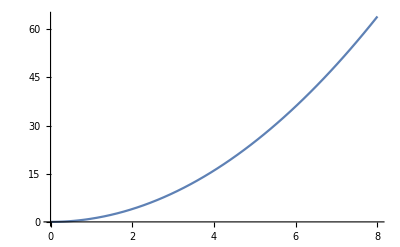

```mathematica
Plot[y[x], {x, 0, 8}]
```

```mathematica
preciselengthOfCurve[y, {0, 8}, 10]
```

64.8087

### IV. Investigate the arclength of families of functions

```mathematica
i
```

```mathematica
f[x_]:=a Sin[x]
```

{{1,3.79009},{2,5.19492},{3,6.88115},{4,8.69184},{5,10.567},{6,12.4792},{7,14.4144},{8,16.3648},{9,18.3256},{10,20.2939},{11,22.2678},{12,24.2459},{13,26.2273},{14,28.2113},{15,30.1974}}

2.16844+1.45943 x+0.0519359 x^2-0.00166011 x^3

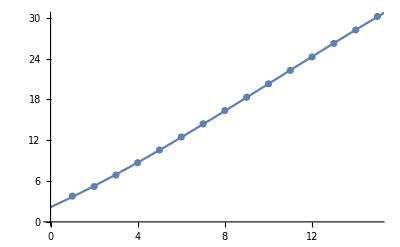

```mathematica
list=Table[{a,preciselengthOfCurve[f, {0,π},6]}, {a,1, 15}]
model=Fit[list,{1, x, x^2, x^3}, x]
Show[ListPlot[list], Plot[model, {x, 0, 16}]]
```

```mathematica
ii
```

{{1,3.81897},{2,8.78457},{3,18.2911},{4,31.1718},{5,50.1189},{6,69.7602},{7,93.329},{8,121.787},{9,149.056},{10,200.025},{11,213.261},{12,239.673},{13,282.582},{14,318.984},{15,362.148}}

1.70046-1.29715 x+2.46752 x^2-0.0532491 x^3

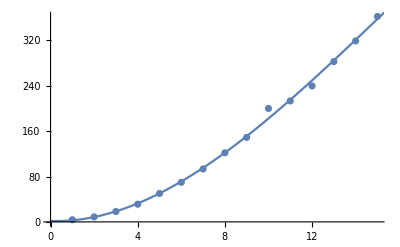

```mathematica
num=1;
list={};
While[num<16,
f[x_]:=num Sin[num x];
update=N@lengthOfCurve[f, {0,π}, 20];
AppendTo[list, {num, update}];
num++;
]
list
model=Fit[list, {1, x, x^2, x^3},x]
Show[ListPlot[list], Plot[model, {x, 0, 16}]]
```

```mathematica
iii
```

```mathematica
bound=1;
num=1;
list={};
While[num<16,
f[x_]:=2*√(-2 x^2+ 2 num^2);
update=N@lengthOfCurve[f, {-num, num}, 15];
AppendTo[list, {num, update}];
num++;
]
list
model=Fit[list, {1, x, x^2, x^3},x]
Show[ListPlot[list], Plot[model, {x, 0, 15}]]
```

```mathematica
iv
```

{{1,3.12721},{2,7.61607},{3,13.0731},{4,19.3343},{5,26.3002},{6,33.9015},{7,42.0866},{8,50.8146},{9,60.0525},{10,69.7726},{11,79.9514},{12,90.5685},{13,101.606},{14,113.048},{15,124.881}}

-0.95255+3.52154 x+0.416926 x^2-0.00619107 x^3

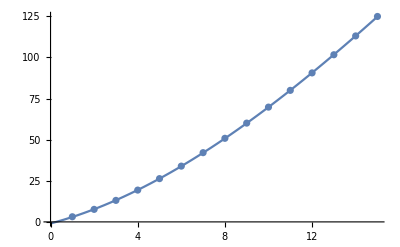

```mathematica
num=1;
list={};
While[num<16,
f[x_]:=√(num^3-num x^2);
update=N@lengthOfCurve[f, {-num, num},15];
AppendTo[list, {num, update}];
num++
]
list
model =Fit[list, {1, x, x^2, x^3}, x]
Show[ListPlot[list], Plot[model, {x, 0, 15}]]
```

```mathematica
v
```

{{1,3.12721},{2,11.0116+0. ⅈ},{3,24.0885+0. ⅈ},{4,36.7521+0. ⅈ},{5,59.864+0. ⅈ},{6,78.2368+0. ⅈ},{7,103.537+0. ⅈ},{8,133.073+0. ⅈ},{9,166.67+0. ⅈ},{10,204.274+0. ⅈ},{11,245.861+0. ⅈ},{12,291.421+0. ⅈ},{13,340.947+0. ⅈ},{14,394.435+0. ⅈ},{15,451.883+0. ⅈ}}

-1.96375+3.6108 x+1.54827 x^2+0.015381 x^3

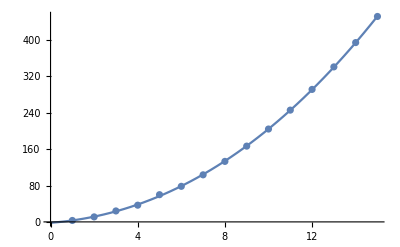

```mathematica
num=1;
list={};
While[num<16,
f[x_]:=√(-num^2 x^2+num^2);
update=N@lengthOfCurve[f, {-num, num}, 15];
AppendTo[list, {num, update}];
num++;
]
list
model=Fit[list, {1, x, x^2, x^3}, x]
Show[ListPlot[list], Plot[model, {x, 0, 15}]]
```

```mathematica
f[x_]:=Sin[x];
```

```mathematica
findPoints[f, {-π/4., 10π/13}, 10]
```

{{-0.785398,-0.707107},{-0.465197,-0.448599},{-0.144997,-0.144489},{0.175204,0.174309},{0.495405,0.475388},{0.815606,0.728141},{1.13581,0.906874},{1.45601,0.993419},{1.77621,0.978977},{2.09641,0.865017},{2.41661,0.663123}}

```mathematica
Length@{{-0.785398, -0.707107}, {-0.465197, -0.448599}, {-0.144997, -0.144489}, {0.175204, 0.174309}, {0.495405, 0.475388}, {0.815606, 0.728141}, {1.13581, 0.906874}, {1.45601, 0.993419}, {1.77621, 0.978977}, {2.09641, 0.865017}, {2.41661, 0.663123}}
```

11

```mathematica
preciselengthOfCurve[f, {-π/4., 10π/13}, 2]
```

3.75247

```mathematica
f[x_]:=Cos[4 x]^2
```

```mathematica
preciselengthOfCurve[f, {1., 20}, 5]
```

19.005